```mathematica
$Version
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

14.0.0 for Microsoft Windows (64-bit) (December 13, 2023)

C:\Users\Austin\Documents\fDNLS

```mathematica
LatticeEndIndex = 50;
```

```mathematica
J[n_,α_]:=J[n,α]=1/Abs[n]^(1+α);
K[α_]:=Zeta[1+α];
```

```mathematica
wB = 1/2;
wA = 2 wB;
```

```mathematica
q[0,ϵ_,α_,wA_]:=Sqrt[wA+2 ϵ  K[α]];
q[n_Integer?Positive,ϵ_,α_,wA_]:=q[n,ϵ,α,wA]=ϵ  (J[n,α]*q[0,ϵ,α,wA]+Sum[(J[n-m,α]+J[n+m,α])*q[m,ϵ,α,wA],{m,1,n-1}])/(ϵ  (2K[α]-J[2n,α])+wA)//Simplify
```

```mathematica
g[0,ϵ_,α_,wB_]:=Sqrt[wB+ϵ(2K[α]-J[1,α])]
g[1,ϵ_,α_,wB_]:=Sqrt[wB+ϵ(2K[α]-J[1,α])]
g[n_Integer?Positive,ϵ_,α_,wB_]:=g[n,ϵ,α,wB]= ϵ Sum[(J[n-m,α]+J[n+m-1,α])*g[m,ϵ,α,wB],{m,1,n-1}]/(ϵ  (2K[α]-J[2n-1,α])+wB)//Simplify
```

```mathematica
EA[ϵ_,α_,wA_]:=ϵ Sum[1/n^(1+α)Abs[ q[n,ϵ,α,wA] - q[0,ϵ,α,wA] ]^2 + 1/2 Sum[If[m!=n,(1/Abs[n-m]^(1+α)+1/Abs[n+m]^(1+α))*Abs[ q[n,ϵ,α,wA]- q[m,ϵ,α,wA]]^2,0],{m,1,LatticeEndIndex}],{n,1,LatticeEndIndex }]-(1/4 q[0,ϵ,α,wA]^4+1/2 Sum[q[n,ϵ,α,wA]^4,{n,1,LatticeEndIndex }])
```

```mathematica
EB[ϵ_,α_,wB_]:= ϵ Sum[(1/n^(1+α)+1/(n-1)^(1+α))Abs[g[n,ϵ,α,wB] - g[0,ϵ,α,wB]]^2+1/2 Sum[If[m!=n,(1/Abs[n-m]^(1+α)+1/Abs[n+m-1]^(1+α))*Abs[g[n,ϵ,α,wB]-g[m,ϵ,α,wB]]^2,0],{m,2,LatticeEndIndex}],{n,2,LatticeEndIndex}]-1/2 Sum[g[n,ϵ,α,wB]^4,{n,1,LatticeEndIndex}]
```

```mathematica
onsiteSequence=q[#,0.496,1,1]&/@Range[0,LatticeEndIndex];
offsiteSequence=g[#,0.496,1,1]&/@Range[0,LatticeEndIndex];
```

```mathematica
Length[onsiteSequence]
```

51

```mathematica
Length[offsiteSequence]
```

51

```mathematica
onsiteSequence = Catenate[{Reverse[onsiteSequence[[2;;Length[onsiteSequence]]]],onsiteSequence[[1;;Length[onsiteSequence]]]}];
```

```mathematica
Length[onsiteSequence]
```

101

```mathematica
offsiteSequence = Catenate[{Reverse[offsiteSequence[[3;;Length[offsiteSequence]]]],offsiteSequence[[1;;Length[offsiteSequence]]]}];
```

```mathematica
Length[offsiteSequence]
```

100

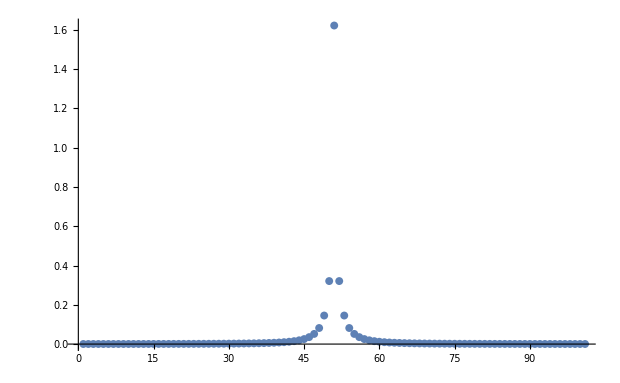

```mathematica
ListPlot[onsiteSequence , PlotRange->All]
```

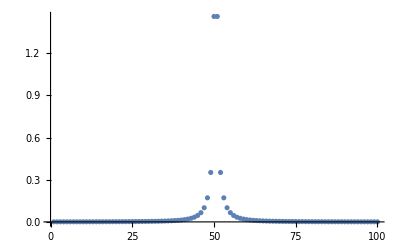

```mathematica
ListPlot[offsiteSequence , PlotRange->All]
```

```mathematica
Length[onsiteSequence]
```

101

```mathematica
Length[offsiteSequence]
```

100

```mathematica
Export["onsiteSequence.mat",onsiteSequence]
Export["offsiteSequence.mat",offsiteSequence]
```

onsiteSequence.mat

offsiteSequence.mat

```mathematica
data = Table[{ϵ, EA[ϵ,1,wA]-EB[ϵ,1,wB]}, {ϵ, 0, 1,0.001}];
```

```mathematica
data//N
```

{{0.,-0.125},{0.001,-0.124998},{0.002,-0.124994},{0.003,-0.124987},{0.004,-0.124977},{0.005,-0.124964},{0.006,-0.124949},{0.007,-0.124932},{0.008,-0.124912},{0.009,-0.124889},{0.01,-0.124864},{0.011,-0.124837},{0.012,-0.124807},{0.013,-0.124775},{0.014,-0.124741},{0.015,-0.124705},{0.016,-0.124667},{0.017,-0.124626},{0.018,-0.124584},{0.019,-0.124539},{0.02,-0.124493},{0.021,-0.124444},{0.022,-0.124394},{0.023,-0.124341},{0.024,-0.124287},{0.025,-0.124231},{0.026,-0.124173},{0.027,-0.124113},{0.028,-0.124052},{0.029,-0.123989},{0.03,-0.123924},{0.031,-0.123857},{0.032,-0.123789},{0.033,-0.123719},{0.034,-0.123647},{0.035,-0.123574},{0.036,-0.1235},{0.037,-0.123423},{0.038,-0.123346},{0.039,-0.123266},{0.04,-0.123185},{0.041,-0.123103},{0.042,-0.123019},{0.043,-0.122934},{0.044,-0.122847},{0.045,-0.122759},{0.046,-0.12267},{0.047,-0.122579},{0.048,-0.122487},{0.049,-0.122393},{0.05,-0.122298},{0.051,-0.122202},{0.052,-0.122104},{0.053,-0.122005},{0.054,-0.121905},{0.055,-0.121804},{0.056,-0.121701},{0.057,-0.121597},{0.058,-0.121492},{0.059,-0.121385},{0.06,-0.121278},{0.061,-0.121169},{0.062,-0.121059},{0.063,-0.120947},{0.064,-0.120835},{0.065,-0.120721},{0.066,-0.120607},{0.067,-0.120491},{0.068,-0.120374},{0.069,-0.120256},{0.07,-0.120136},{0.071,-0.120016},{0.072,-0.119894},{0.073,-0.119772},{0.074,-0.119648},{0.075,-0.119523},{0.076,-0.119398},{0.077,-0.119271},{0.078,-0.119143},{0.079,-0.119014},{0.08,-0.118884},{0.081,-0.118753},{0.082,-0.11862},{0.083,-0.118487},{0.084,-0.118353},{0.085,-0.118218},{0.086,-0.118082},{0.087,-0.117945},{0.088,-0.117807},{0.089,-0.117667},{0.09,-0.117527},{0.091,-0.117386},{0.092,-0.117244},{0.093,-0.117101},{0.094,-0.116957},{0.095,-0.116812},{0.096,-0.116666},{0.097,-0.116519},{0.098,-0.116372},{0.099,-0.116223},{0.1,-0.116073},{0.101,-0.115923},{0.102,-0.115771},{0.103,-0.115619},{0.104,-0.115465},{0.105,-0.115311},{0.106,-0.115156},{0.107,-0.115},{0.108,-0.114843},{0.109,-0.114685},{0.11,-0.114526},{0.111,-0.114367},{0.112,-0.114206},{0.113,-0.114045},{0.114,-0.113883},{0.115,-0.113719},{0.116,-0.113555},{0.117,-0.113391},{0.118,-0.113225},{0.119,-0.113058},{0.12,-0.112891},{0.121,-0.112723},{0.122,-0.112553},{0.123,-0.112383},{0.124,-0.112213},{0.125,-0.112041},{0.126,-0.111868},{0.127,-0.111695},{0.128,-0.111521},{0.129,-0.111346},{0.13,-0.11117},{0.131,-0.110993},{0.132,-0.110816},{0.133,-0.110638},{0.134,-0.110458},{0.135,-0.110279},{0.136,-0.110098},{0.137,-0.109916},{0.138,-0.109734},{0.139,-0.109551},{0.14,-0.109367},{0.141,-0.109182},{0.142,-0.108996},{0.143,-0.10881},{0.144,-0.108623},{0.145,-0.108435},{0.146,-0.108246},{0.147,-0.108057},{0.148,-0.107866},{0.149,-0.107675},{0.15,-0.107483},{0.151,-0.107291},{0.152,-0.107097},{0.153,-0.106903},{0.154,-0.106708},{0.155,-0.106512},{0.156,-0.106316},{0.157,-0.106119},{0.158,-0.105921},{0.159,-0.105722},{0.16,-0.105522},{0.161,-0.105322},{0.162,-0.105121},{0.163,-0.104919},{0.164,-0.104716},{0.165,-0.104513},{0.166,-0.104309},{0.167,-0.104104},{0.168,-0.103898},{0.169,-0.103692},{0.17,-0.103484},{0.171,-0.103277},{0.172,-0.103068},{0.173,-0.102859},{0.174,-0.102648},{0.175,-0.102437},{0.176,-0.102226},{0.177,-0.102014},{0.178,-0.1018},{0.179,-0.101587},{0.18,-0.101372},{0.181,-0.101157},{0.182,-0.100941},{0.183,-0.100724},{0.184,-0.100506},{0.185,-0.100288},{0.186,-0.100069},{0.187,-0.0998496},{0.188,-0.0996292},{0.189,-0.099408},{0.19,-0.0991862},{0.191,-0.0989636},{0.192,-0.0987403},{0.193,-0.0985163},{0.194,-0.0982915},{0.195,-0.0980661},{0.196,-0.0978399},{0.197,-0.097613},{0.198,-0.0973854},{0.199,-0.0971571},{0.2,-0.096928},{0.201,-0.0966983},{0.202,-0.0964678},{0.203,-0.0962367},{0.204,-0.0960048},{0.205,-0.0957722},{0.206,-0.0955389},{0.207,-0.0953049},{0.208,-0.0950702},{0.209,-0.0948347},{0.21,-0.0945986},{0.211,-0.0943618},{0.212,-0.0941243},{0.213,-0.093886},{0.214,-0.0936471},{0.215,-0.0934075},{0.216,-0.0931672},{0.217,-0.0929261},{0.218,-0.0926844},{0.219,-0.092442},{0.22,-0.0921989},{0.221,-0.091955},{0.222,-0.0917105},{0.223,-0.0914653},{0.224,-0.0912194},{0.225,-0.0909728},{0.226,-0.0907256},{0.227,-0.0904776},{0.228,-0.0902289},{0.229,-0.0899796},{0.23,-0.0897295},{0.231,-0.0894788},{0.232,-0.0892274},{0.233,-0.0889753},{0.234,-0.0887225},{0.235,-0.088469},{0.236,-0.0882149},{0.237,-0.08796},{0.238,-0.0877045},{0.239,-0.0874483},{0.24,-0.0871914},{0.241,-0.0869338},{0.242,-0.0866756},{0.243,-0.0864166},{0.244,-0.086157},{0.245,-0.0858967},{0.246,-0.0856357},{0.247,-0.0853741},{0.248,-0.0851117},{0.249,-0.0848487},{0.25,-0.0845851},{0.251,-0.0843207},{0.252,-0.0840557},{0.253,-0.08379},{0.254,-0.0835236},{0.255,-0.0832565},{0.256,-0.0829888},{0.257,-0.0827204},{0.258,-0.0824513},{0.259,-0.0821816},{0.26,-0.0819112},{0.261,-0.0816401},{0.262,-0.0813683},{0.263,-0.0810959},{0.264,-0.0808228},{0.265,-0.080549},{0.266,-0.0802746},{0.267,-0.0799995},{0.268,-0.0797237},{0.269,-0.0794473},{0.27,-0.0791702},{0.271,-0.0788925},{0.272,-0.078614},{0.273,-0.0783349},{0.274,-0.0780552},{0.275,-0.0777748},{0.276,-0.0774937},{0.277,-0.0772119},{0.278,-0.0769295},{0.279,-0.0766465},{0.28,-0.0763627},{0.281,-0.0760783},{0.282,-0.0757933},{0.283,-0.0755076},{0.284,-0.0752212},{0.285,-0.0749342},{0.286,-0.0746465},{0.287,-0.0743581},{0.288,-0.0740691},{0.289,-0.0737795},{0.29,-0.0734892},{0.291,-0.0731982},{0.292,-0.0729065},{0.293,-0.0726143},{0.294,-0.0723213},{0.295,-0.0720277},{0.296,-0.0717335},{0.297,-0.0714386},{0.298,-0.071143},{0.299,-0.0708468},{0.3,-0.0705499},{0.301,-0.0702524},{0.302,-0.0699542},{0.303,-0.0696554},{0.304,-0.0693559},{0.305,-0.0690558},{0.306,-0.068755},{0.307,-0.0684536},{0.308,-0.0681515},{0.309,-0.0678487},{0.31,-0.0675454},{0.311,-0.0672413},{0.312,-0.0669367},{0.313,-0.0666313},{0.314,-0.0663253},{0.315,-0.0660187},{0.316,-0.0657114},{0.317,-0.0654035},{0.318,-0.065095},{0.319,-0.0647857},{0.32,-0.0644759},{0.321,-0.0641654},{0.322,-0.0638542},{0.323,-0.0635424},{0.324,-0.06323},{0.325,-0.0629169},{0.326,-0.0626032},{0.327,-0.0622888},{0.328,-0.0619738},{0.329,-0.0616581},{0.33,-0.0613418},{0.331,-0.0610249},{0.332,-0.0607073},{0.333,-0.060389},{0.334,-0.0600702},{0.335,-0.0597506},{0.336,-0.0594305},{0.337,-0.0591097},{0.338,-0.0587882},{0.339,-0.0584661},{0.34,-0.0581434},{0.341,-0.0578201},{0.342,-0.0574961},{0.343,-0.0571714},{0.344,-0.0568461},{0.345,-0.0565202},{0.346,-0.0561937},{0.347,-0.0558665},{0.348,-0.0555386},{0.349,-0.0552102},{0.35,-0.054881},{0.351,-0.0545513},{0.352,-0.0542209},{0.353,-0.0538899},{0.354,-0.0535582},{0.355,-0.0532259},{0.356,-0.052893},{0.357,-0.0525594},{0.358,-0.0522252},{0.359,-0.0518904},{0.36,-0.0515549},{0.361,-0.0512188},{0.362,-0.0508821},{0.363,-0.0505447},{0.364,-0.0502067},{0.365,-0.049868},{0.366,-0.0495288},{0.367,-0.0491888},{0.368,-0.0488483},{0.369,-0.0485071},{0.37,-0.0481653},{0.371,-0.0478229},{0.372,-0.0474798},{0.373,-0.0471361},{0.374,-0.0467918},{0.375,-0.0464468},{0.376,-0.0461012},{0.377,-0.0457549},{0.378,-0.0454081},{0.379,-0.0450606},{0.38,-0.0447125},{0.381,-0.0443637},{0.382,-0.0440143},{0.383,-0.0436643},{0.384,-0.0433137},{0.385,-0.0429624},{0.386,-0.0426105},{0.387,-0.042258},{0.388,-0.0419048},{0.389,-0.041551},{0.39,-0.0411966},{0.391,-0.0408416},{0.392,-0.0404859},{0.393,-0.0401296},{0.394,-0.0397727},{0.395,-0.0394151},{0.396,-0.0390569},{0.397,-0.0386981},{0.398,-0.0383387},{0.399,-0.0379786},{0.4,-0.0376179},{0.401,-0.0372566},{0.402,-0.0368947},{0.403,-0.0365321},{0.404,-0.0361689},{0.405,-0.0358051},{0.406,-0.0354406},{0.407,-0.0350756},{0.408,-0.0347099},{0.409,-0.0343436},{0.41,-0.0339766},{0.411,-0.0336091},{0.412,-0.0332409},{0.413,-0.0328721},{0.414,-0.0325026},{0.415,-0.0321326},{0.416,-0.0317619},{0.417,-0.0313906},{0.418,-0.0310187},{0.419,-0.0306461},{0.42,-0.0302729},{0.421,-0.0298991},{0.422,-0.0295247},{0.423,-0.0291497},{0.424,-0.028774},{0.425,-0.0283977},{0.426,-0.0280208},{0.427,-0.0276433},{0.428,-0.0272651},{0.429,-0.0268864},{0.43,-0.026507},{0.431,-0.026127},{0.432,-0.0257463},{0.433,-0.0253651},{0.434,-0.0249832},{0.435,-0.0246007},{0.436,-0.0242176},{0.437,-0.0238339},{0.438,-0.0234495},{0.439,-0.0230646},{0.44,-0.022679},{0.441,-0.0222928},{0.442,-0.0219059},{0.443,-0.0215185},{0.444,-0.0211304},{0.445,-0.0207417},{0.446,-0.0203524},{0.447,-0.0199625},{0.448,-0.019572},{0.449,-0.0191808},{0.45,-0.0187891},{0.451,-0.0183967},{0.452,-0.0180037},{0.453,-0.01761},{0.454,-0.0172158},{0.455,-0.0168209},{0.456,-0.0164255},{0.457,-0.0160294},{0.458,-0.0156327},{0.459,-0.0152353},{0.46,-0.0148374},{0.461,-0.0144388},{0.462,-0.0140397},{0.463,-0.0136399},{0.464,-0.0132395},{0.465,-0.0128384},{0.466,-0.0124368},{0.467,-0.0120346},{0.468,-0.0116317},{0.469,-0.0112282},{0.47,-0.0108241},{0.471,-0.0104194},{0.472,-0.0100141},{0.473,-0.00960815},{0.474,-0.00920159},{0.475,-0.00879443},{0.476,-0.00838665},{0.477,-0.00797825},{0.478,-0.00756924},{0.479,-0.00715962},{0.48,-0.00674939},{0.481,-0.00633854},{0.482,-0.00592708},{0.483,-0.005515},{0.484,-0.00510232},{0.485,-0.00468902},{0.486,-0.0042751},{0.487,-0.00386058},{0.488,-0.00344544},{0.489,-0.00302969},{0.49,-0.00261333},{0.491,-0.00219636},{0.492,-0.00177877},{0.493,-0.00136058},{0.494,-0.000941767},{0.495,-0.000522347},{0.496,-0.000102315},{0.497,0.000318327},{0.498,0.000739581},{0.499,0.00116145},{0.5,0.00158392},{0.501,0.00200701},{0.502,0.00243071},{0.503,0.00285501},{0.504,0.00327993},{0.505,0.00370546},{0.506,0.0041316},{0.507,0.00455835},{0.508,0.0049857},{0.509,0.00541367},{0.51,0.00584225},{0.511,0.00627144},{0.512,0.00670123},{0.513,0.00713164},{0.514,0.00756265},{0.515,0.00799428},{0.516,0.00842651},{0.517,0.00885935},{0.518,0.00929281},{0.519,0.00972687},{0.52,0.0101615},{0.521,0.0105968},{0.522,0.0110327},{0.523,0.0114692},{0.524,0.0119063},{0.525,0.012344},{0.526,0.0127823},{0.527,0.0132212},{0.528,0.0136608},{0.529,0.0141009},{0.53,0.0145417},{0.531,0.014983},{0.532,0.015425},{0.533,0.0158675},{0.534,0.0163107},{0.535,0.0167545},{0.536,0.0171989},{0.537,0.0176439},{0.538,0.0180895},{0.539,0.0185357},{0.54,0.0189825},{0.541,0.0194299},{0.542,0.019878},{0.543,0.0203266},{0.544,0.0207758},{0.545,0.0212257},{0.546,0.0216761},{0.547,0.0221272},{0.548,0.0225789},{0.549,0.0230311},{0.55,0.023484},{0.551,0.0239375},{0.552,0.0243916},{0.553,0.0248463},{0.554,0.0253016},{0.555,0.0257575},{0.556,0.026214},{0.557,0.0266711},{0.558,0.0271288},{0.559,0.0275871},{0.56,0.028046},{0.561,0.0285056},{0.562,0.0289657},{0.563,0.0294264},{0.564,0.0298878},{0.565,0.0303497},{0.566,0.0308123},{0.567,0.0312754},{0.568,0.0317392},{0.569,0.0322035},{0.57,0.0326685},{0.571,0.033134},{0.572,0.0336002},{0.573,0.034067},{0.574,0.0345344},{0.575,0.0350023},{0.576,0.0354709},{0.577,0.0359401},{0.578,0.0364099},{0.579,0.0368803},{0.58,0.0373513},{0.581,0.0378229},{0.582,0.0382951},{0.583,0.0387679},{0.584,0.0392413},{0.585,0.0397153},{0.586,0.0401899},{0.587,0.0406651},{0.588,0.0411409},{0.589,0.0416173},{0.59,0.0420943},{0.591,0.0425719},{0.592,0.0430502},{0.593,0.043529},{0.594,0.0440084},{0.595,0.0444884},{0.596,0.044969},{0.597,0.0454503},{0.598,0.0459321},{0.599,0.0464145},{0.6,0.0468975},{0.601,0.0473812},{0.602,0.0478654},{0.603,0.0483502},{0.604,0.0488356},{0.605,0.0493217},{0.606,0.0498083},{0.607,0.0502955},{0.608,0.0507834},{0.609,0.0512718},{0.61,0.0517608},{0.611,0.0522504},{0.612,0.0527407},{0.613,0.0532315},{0.614,0.0537229},{0.615,0.054215},{0.616,0.0547076},{0.617,0.0552008},{0.618,0.0556947},{0.619,0.0561891},{0.62,0.0566841},{0.621,0.0571797},{0.622,0.057676},{0.623,0.0581728},{0.624,0.0586702},{0.625,0.0591682},{0.626,0.0596669},{0.627,0.0601661},{0.628,0.0606659},{0.629,0.0611663},{0.63,0.0616673},{0.631,0.0621689},{0.632,0.0626712},{0.633,0.063174},{0.634,0.0636774},{0.635,0.0641814},{0.636,0.064686},{0.637,0.0651912},{0.638,0.065697},{0.639,0.0662034},{0.64,0.0667104},{0.641,0.067218},{0.642,0.0677262},{0.643,0.068235},{0.644,0.0687444},{0.645,0.0692543},{0.646,0.0697649},{0.647,0.0702761},{0.648,0.0707879},{0.649,0.0713003},{0.65,0.0718132},{0.651,0.0723268},{0.652,0.072841},{0.653,0.0733557},{0.654,0.0738711},{0.655,0.074387},{0.656,0.0749036},{0.657,0.0754208},{0.658,0.0759385},{0.659,0.0764568},{0.66,0.0769758},{0.661,0.0774953},{0.662,0.0780155},{0.663,0.0785362},{0.664,0.0790575},{0.665,0.0795794},{0.666,0.0801019},{0.667,0.0806251},{0.668,0.0811488},{0.669,0.0816731},{0.67,0.082198},{0.671,0.0827235},{0.672,0.0832496},{0.673,0.0837763},{0.674,0.0843035},{0.675,0.0848314},{0.676,0.0853599},{0.677,0.085889},{0.678,0.0864186},{0.679,0.0869489},{0.68,0.0874797},{0.681,0.0880112},{0.682,0.0885432},{0.683,0.0890759},{0.684,0.0896091},{0.685,0.090143},{0.686,0.0906774},{0.687,0.0912124},{0.688,0.091748},{0.689,0.0922842},{0.69,0.092821},{0.691,0.0933584},{0.692,0.0938964},{0.693,0.094435},{0.694,0.0949742},{0.695,0.095514},{0.696,0.0960543},{0.697,0.0965953},{0.698,0.0971369},{0.699,0.097679},{0.7,0.0982218},{0.701,0.0987651},{0.702,0.099309},{0.703,0.0998536},{0.704,0.100399},{0.705,0.100944},{0.706,0.101491},{0.707,0.102038},{0.708,0.102585},{0.709,0.103133},{0.71,0.103682},{0.711,0.104231},{0.712,0.104781},{0.713,0.105332},{0.714,0.105883},{0.715,0.106434},{0.716,0.106986},{0.717,0.107539},{0.718,0.108093},{0.719,0.108647},{0.72,0.109201},{0.721,0.109757},{0.722,0.110312},{0.723,0.110869},{0.724,0.111426},{0.725,0.111983},{0.726,0.112541},{0.727,0.1131},{0.728,0.11366},{0.729,0.11422},{0.73,0.11478},{0.731,0.115341},{0.732,0.115903},{0.733,0.116465},{0.734,0.117028},{0.735,0.117592},{0.736,0.118156},{0.737,0.11872},{0.738,0.119286},{0.739,0.119852},{0.74,0.120418},{0.741,0.120985},{0.742,0.121553},{0.743,0.122121},{0.744,0.12269},{0.745,0.123259},{0.746,0.123829},{0.747,0.1244},{0.748,0.124971},{0.749,0.125543},{0.75,0.126115},{0.751,0.126688},{0.752,0.127262},{0.753,0.127836},{0.754,0.128411},{0.755,0.128986},{0.756,0.129562},{0.757,0.130138},{0.758,0.130716},{0.759,0.131293},{0.76,0.131871},{0.761,0.13245},{0.762,0.13303},{0.763,0.13361},{0.764,0.134191},{0.765,0.134772},{0.766,0.135354},{0.767,0.135936},{0.768,0.136519},{0.769,0.137103},{0.77,0.137687},{0.771,0.138272},{0.772,0.138857},{0.773,0.139443},{0.774,0.14003},{0.775,0.140617},{0.776,0.141204},{0.777,0.141793},{0.778,0.142382},{0.779,0.142971},{0.78,0.143561},{0.781,0.144152},{0.782,0.144743},{0.783,0.145335},{0.784,0.145928},{0.785,0.146521},{0.786,0.147114},{0.787,0.147708},{0.788,0.148303},{0.789,0.148899},{0.79,0.149495},{0.791,0.150091},{0.792,0.150688},{0.793,0.151286},{0.794,0.151884},{0.795,0.152483},{0.796,0.153083},{0.797,0.153683},{0.798,0.154284},{0.799,0.154885},{0.8,0.155487},{0.801,0.156089},{0.802,0.156692},{0.803,0.157296},{0.804,0.1579},{0.805,0.158505},{0.806,0.159111},{0.807,0.159717},{0.808,0.160323},{0.809,0.16093},{0.81,0.161538},{0.811,0.162146},{0.812,0.162755},{0.813,0.163365},{0.814,0.163975},{0.815,0.164586},{0.816,0.165197},{0.817,0.165809},{0.818,0.166421},{0.819,0.167034},{0.82,0.167648},{0.821,0.168262},{0.822,0.168877},{0.823,0.169493},{0.824,0.170109},{0.825,0.170725},{0.826,0.171342},{0.827,0.17196},{0.828,0.172579},{0.829,0.173197},{0.83,0.173817},{0.831,0.174437},{0.832,0.175058},{0.833,0.175679},{0.834,0.176301},{0.835,0.176923},{0.836,0.177547},{0.837,0.17817},{0.838,0.178794},{0.839,0.179419},{0.84,0.180045},{0.841,0.180671},{0.842,0.181297},{0.843,0.181924},{0.844,0.182552},{0.845,0.18318},{0.846,0.183809},{0.847,0.184439},{0.848,0.185069},{0.849,0.1857},{0.85,0.186331},{0.851,0.186963},{0.852,0.187595},{0.853,0.188228},{0.854,0.188862},{0.855,0.189496},{0.856,0.190131},{0.857,0.190766},{0.858,0.191402},{0.859,0.192039},{0.86,0.192676},{0.861,0.193314},{0.862,0.193952},{0.863,0.194591},{0.864,0.195231},{0.865,0.195871},{0.866,0.196511},{0.867,0.197153},{0.868,0.197794},{0.869,0.198437},{0.87,0.19908},{0.871,0.199723},{0.872,0.200368},{0.873,0.201012},{0.874,0.201658},{0.875,0.202304},{0.876,0.20295},{0.877,0.203597},{0.878,0.204245},{0.879,0.204893},{0.88,0.205542},{0.881,0.206192},{0.882,0.206842},{0.883,0.207492},{0.884,0.208144},{0.885,0.208795},{0.886,0.209448},{0.887,0.210101},{0.888,0.210754},{0.889,0.211408},{0.89,0.212063},{0.891,0.212718},{0.892,0.213374},{0.893,0.214031},{0.894,0.214688},{0.895,0.215346},{0.896,0.216004},{0.897,0.216663},{0.898,0.217322},{0.899,0.217982},{0.9,0.218643},{0.901,0.219304},{0.902,0.219966},{0.903,0.220628},{0.904,0.221291},{0.905,0.221954},{0.906,0.222618},{0.907,0.223283},{0.908,0.223948},{0.909,0.224614},{0.91,0.225281},{0.911,0.225948},{0.912,0.226615},{0.913,0.227283},{0.914,0.227952},{0.915,0.228622},{0.916,0.229291},{0.917,0.229962},{0.918,0.230633},{0.919,0.231305},{0.92,0.231977},{0.921,0.23265},{0.922,0.233323},{0.923,0.233997},{0.924,0.234672},{0.925,0.235347},{0.926,0.236023},{0.927,0.236699},{0.928,0.237376},{0.929,0.238054},{0.93,0.238732},{0.931,0.239411},{0.932,0.24009},{0.933,0.24077},{0.934,0.24145},{0.935,0.242131},{0.936,0.242813},{0.937,0.243495},{0.938,0.244178},{0.939,0.244862},{0.94,0.245545},{0.941,0.24623},{0.942,0.246915},{0.943,0.247601},{0.944,0.248287},{0.945,0.248974},{0.946,0.249662},{0.947,0.25035},{0.948,0.251038},{0.949,0.251727},{0.95,0.252417},{0.951,0.253108},{0.952,0.253799},{0.953,0.25449},{0.954,0.255182},{0.955,0.255875},{0.956,0.256568},{0.957,0.257262},{0.958,0.257957},{0.959,0.258652},{0.96,0.259347},{0.961,0.260044},{0.962,0.26074},{0.963,0.261438},{0.964,0.262136},{0.965,0.262834},{0.966,0.263534},{0.967,0.264233},{0.968,0.264934},{0.969,0.265634},{0.97,0.266336},{0.971,0.267038},{0.972,0.267741},{0.973,0.268444},{0.974,0.269148},{0.975,0.269852},{0.976,0.270557},{0.977,0.271263},{0.978,0.271969},{0.979,0.272676},{0.98,0.273383},{0.981,0.274091},{0.982,0.274799},{0.983,0.275508},{0.984,0.276218},{0.985,0.276928},{0.986,0.277639},{0.987,0.27835},{0.988,0.279062},{0.989,0.279775},{0.99,0.280488},{0.991,0.281202},{0.992,0.281916},{0.993,0.282631},{0.994,0.283346},{0.995,0.284062},{0.996,0.284779},{0.997,0.285496},{0.998,0.286214},{0.999,0.286932},{1.,0.287651}}

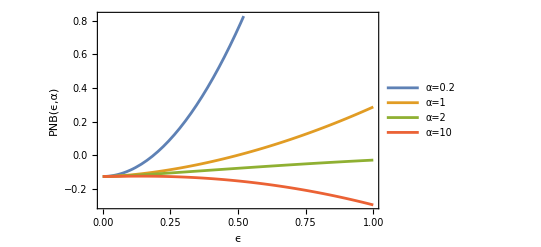

```mathematica
Plot[{EA[ϵ,0.2,wA]-EB[ϵ,0.2,wB],EA[ϵ,1,wA]-EB[ϵ,1,wB],EA[ϵ,2,wA]-EB[ϵ,2,wB],EA[ϵ,10,wA]-EB[ϵ,10,wB]},{ϵ,0,1},PlotLegends->{"α=0.2","α=1","α=2","α=10"},Frame->True,FrameStyle->Thick,FrameLabel->{Style["ϵ",16,Bold],
Rotate[Style["PNB(ϵ,α)",16,Bold], -90 Degree]}]
```